```mathematica
ClearAll["Global`*"]
```

```mathematica
Cb1c[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! CbE2b[n/b^j,a,b],{a,1,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
CbE2b[n_,k_, a_]:= Sum[ Log[j]CbE2b[n/j,k-1,a],{j,2,n}]-a Sum[ Log[j a]CbE2b[n/(a j),k-1,a],{j,1,n/a}];CbE2b[n_,0,a_]:=1
CbE1a[n_,k_, a_]:= CbE1a[n,k,a]=Sum[Log[j]CbE1a[n/j,k-1,a],{j,1,n}]-a Sum[ Log[a j]  CbE1a[n/(a j),k-1,a],{j,1,n/a}];CbE1a[n_,0,a_]:=1
CbDDc[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j CbE1a[n/b^j, k, b],{j,0,Log[b,n]}]
CbE1b[n_,k_,b_]:=Sum[ Binomial[k,j] CbE2b[n,k-j,b],{j,0,k}]
CbDDd[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j CbE1b[n/b^j, k, b],{j,0,Log[b,n]}]
```

```mathematica
N[CbDDc[100,1,2]]
```

-18.8779

```mathematica
N[CbE1a[100,1,200]]
```

363.739

```mathematica
N[CbE1b[100,2,101]]
```

1627.7

```mathematica
N[Sum[ Log[j],{j,1,100}]]
```

363.739

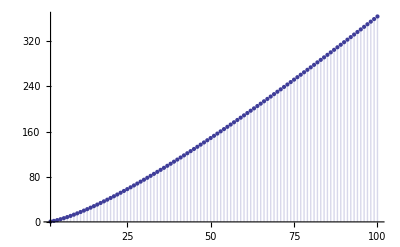

```mathematica
DiscretePlot[CbDDc[n,1,2],{n,2,100}]
```

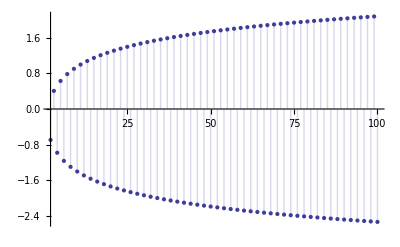

```mathematica
DiscretePlot[ftb3[n,2^0,2],{n,2,100}]
```

```mathematica
t[n_,a_]:=Mod[n,a]-Mod[n-1,a]
f2[n_]:= Sum[ (-1)^(j+1) Log[j],{j,1,n}]
f2b[n_,a_]:= Sum[ (-1)^(j+1) Log[j a],{j,1,n}]
ftb[n_,a_,c_]:= Sum[ t[j,c] Log[j a],{j,1,n}]
f2a[n_] := f[n,1]-2f[n/2,2]
f[n_,a_] := Sum[ Log[j a],{j,1,n}]
f1[n_]:=f2[n]+2f[n/2,2]
f1b[n_]:=f2b[n,1]+2f2b[n/2,2]+4f[n/4,4]
f1c[n_]:=f2b[n,1]+2f2b[n/2,2]+4(f2b[n/4,4]+2f[n/8,8])
f4[n_]:=Sum[ 2^k f2b[n/(2^k),2^k],{k,0,Log[2,n]}]
f43[n_]:=Sum[ 3^k ftb[n/(3^k),3^k,3],{k,0,Log[3,n]}]
f43[n_,s_]:=Sum[ s^k ftb[n/(s^k),s^k,s],{k,0,Log[s,n]}]
ftb1[n_,a_,c_]:= Sum[ t[j,c] (Log[a j]),{j,1,n}]
f431[n_,s_]:=Sum[ s^k ftb1[n/(s^k),s^k,s],{k,0,Log[s,n]}]
ftb2[n_,a_,c_]:= Log[a]Sum[ t[j,c] ,{j,1,n}]+Sum[ t[j,c] (Log[j]),{j,1,n}]
f432[n_,s_]:=Sum[ s^k ftb2[n/(s^k),s^k,s],{k,0,Log[s,n]}]
ftb3[n_,a_,c_]:= Log[a]Mod[n,c]+Sum[ t[j,c] Log[j],{j,2,n}]
f433[n_,b_]:=Sum[ b^k ftb3[Floor[n/(b^k)],b^k,b],{k,0,Log[b,n]}]
ftb1a[n_,a_,c_]:= Sum[ t[j,c] (Log[a j]),{j,1,n}]

ftb4[n_,a_,c_]:= Sum[ (Log[a j]),{j,1,n}]-c Sum[ Log[a c j],{j,1,n/c}]
f434[n_,s_]:=Sum[ s^k ftb4[n/(s^k),s^k,s],{k,0,Log[s,n]}]
```

```mathematica
FullSimplify[ftb1[100,3^0,3]]
```

-96 Log[3]+Log[5279378867581417425990115212984319055708066000]

```mathematica
FullSimplify[ftb1[100,3^1,3]]
```

-95 Log[3]+Log[5279378867581417425990115212984319055708066000]

```mathematica
FullSimplify[ftb1[100,3^2,3]]
```

-94 Log[3]+Log[5279378867581417425990115212984319055708066000]

```mathematica
FullSimplify[ftb1[100,2^2,2]]
```

-97 Log[2]+Log[12611418068195524166851562157]

```mathematica
FullSimplify[ftb4[100,2^2,2]]
```

-97 Log[2]+Log[12611418068195524166851562157]

```mathematica
N[f2[100]]
```

-2.53088

```mathematica
N[CbE1a[100,1,2]]
```

-2.53088

```mathematica
N[f2a[100]]
```

-2.53088

```mathematica
N[f3[100,1]]
```

363.739

```mathematica
N[f4[100]]
```

363.739

```mathematica
N[f1b[100]]
```

363.739

```mathematica
N[f1c[100]]
```

363.739

```mathematica
N[f43[100,2]]
```

363.739

```mathematica
N[f432[100,2]]
```

363.739

```mathematica
N[f433[100,2]]
```

363.739

```mathematica
N[f431[100,2]]
```

```mathematica
363.7393755555634
```

```mathematica
N[f434[100,1.01]]
```

363.739

```mathematica
ss[n_,c_]:=Sum[ t[j,c] ,{j,1,n}]
```

```mathematica
Table[{Mod[n,7]-ss[n,7]},{n,2,100}]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
Mod[1323,3]
```

0

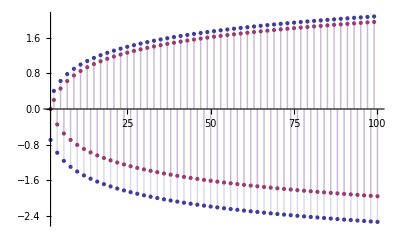

```mathematica
DiscretePlot[{ftb3[n,2^0,2],(-1)^(n+1)Log[n/2]/2},{n,2,100}]
```

```mathematica
ftb4[n_,a_,c_]:= Sum[ (Log[a j]),{j,1,n}]-c Sum[ Log[a c j],{j,1,n/c}]
f434[n_,s_]:=Sum[ s^k ftb4[n/(s^k),s^k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f434[100,1.01]]
```

363.739

```mathematica
N[Sum[Log[j],{j,1,100}]]
```

363.739

```mathematica
ftb5[n_,a_,c_]:= Sum[ (Log[c^a]+Log[j]),{j,1,n}]-c Sum[ Log[c^a]+Log[c]+Log[j],{j,1,n/c}]
f435[n_,s_]:=Sum[ s^k ftb5[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f435[100,1.01]]
```

363.739

```mathematica
ftb6[n_,a_,c_]:= Sum[ (a Log[c]+Log[j]),{j,1,n}]-c Sum[ a Log[c]+Log[c]+Log[j],{j,1,n/c}]
f436[n_,s_]:=Sum[ s^k ftb6[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f436[100,1.01]]
```

363.739

```mathematica
ftb7[n_,a_,c_]:= Sum[ (a Log[c]),{j,1,n}]+Sum[ (Log[j]),{j,1,n}]-c Sum[ (a+1) Log[c],{j,1,n/c}]-c Sum[ Log[j],{j,1,n/c}]
f437[n_,s_]:=Sum[ s^k ftb7[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f437[100,1.01]]
```

363.739

```mathematica
ftb8[n_,a_,c_]:= (a Log[c])Floor[n]+Sum[ (Log[j]),{j,1,n}]-(a+1) Log[c]c Floor[n/c]-c Sum[ Log[j],{j,1,n/c}]
f438[n_,s_]:=Sum[ s^k ftb8[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f438[100,1.01]]
```

363.739

```mathematica
ftb9[n_,a_,c_]:= a Log[c]Floor[n]+Sum[ (Log[j]),{j,1,n}]-(a+1) Log[c]c Floor[n/c]-c Sum[ Log[j],{j,1,n/c}]
f439[n_,s_]:=Sum[ s^k ftb9[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f439[100,1.01]]
```

363.739

```mathematica
FullSimplify[Expand[(a Log[c]Floor[n]-(a+1) Log[c]c Floor[n/c])]]
```

(a Floor[n]-(1+a) c Floor[n/c]) Log[c]

```mathematica
ftb10[n_,a_,c_]:= (a Floor[n]-(1+a) c Floor[n/c]) Log[c]+Sum[ (Log[j]),{j,1,n}]-c Sum[ Log[j],{j,1,n/c}]
f4310[n_,s_]:=Sum[ s^k ftb10[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f4310[100,1.01]]
```

363.739

```mathematica
ftb11[n_,k_,s_]:= (k Floor[n]-(1+k) s Floor[n/s]) Log[s]+Sum[ (Log[j]),{j,1,n}]-s Sum[ Log[j],{j,1,n/s}]
f4311[n_,s_]:=Sum[ s^k ftb11[n/(s^k),k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f4311[100,1.01]]
```

363.739

```mathematica
ftb12[n_,k_,s_]:= (k Floor[n/(s^k)]-(1+k) s Floor[n/(s^k)/s]) Log[s]+Sum[ (Log[j]),{j,1,n/(s^k)}]-s Sum[ Log[j],{j,1,n/(s^k)/s}]
f4312[n_,s_]:=Sum[ s^k ftb12[n,k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f4312[100,1.01]]
```

363.739

```mathematica
ftb13[n_,k_,s_]:= (k Floor[n/(s^k)]-(1+k) s Floor[n/(s^(k+1))]) Log[s]+Sum[ (Log[j]),{j,1,n/(s^k)}]-s Sum[ Log[j],{j,1,n/(s^(k+1))}]
f4313[n_,s_]:=Sum[ s^k ftb13[n,k,s],{k,0,Log[s,n]}]
```

```mathematica
N[f4313[100,1.01]]
```

363.739

```mathematica
ftb14[n_,k_,s_]:= (k Floor[n/(s^k)]-(1+k) s Floor[n/(s^(k+1))]) Log[s]+Sum[ (Log[j]),{j,1,n/(s^k)}]-s Sum[ Log[j],{j,1,n/(s^(k+1))}]
f4314[n_,s_]:=Sum[ s^k ((k Floor[n/(s^k)]-(1+k) s Floor[n/(s^(k+1))]) Log[s]+Sum[ (Log[j]),{j,1,n/(s^k)}]-s Sum[ Log[j],{j,1,n/(s^(k+1))}]),{k,0,Log[s,n]}]
```

```mathematica
N[f4314[100,1.01]]
```

363.739

```mathematica
f4315[n_,s_]:=Sum[ s^k 
((k Floor[n/(s^k)]-(1+k) s Floor[n/(s^(k+1))]) Log[s])
+s^k(Sum[ (Log[j]),{j,1,n/(s^k)}]-s Sum[ Log[j],{j,1,n/(s^(k+1))}]),
{k,0,Log[s,n]}]
```

```mathematica
N[f4315[100,1.01]]
```

363.739

```mathematica
f4316[n_,s_]:=Sum[ s^k 
(k Floor[n/s^k]-(1+k)s Floor[n/s^(k+1)]) Log[s]
+s^k(Sum[ (Log[j]),{j,1,n/(s^k)}]-s Sum[ Log[j],{j,1,n/(s^(k+1))}]),

{k,0,Log[s,n]}]
```

```mathematica
N[f4316[100,1.01]]
```

363.739

```mathematica
f4317[n_,s_]:=Sum[ 
k Floor[n/s^k]Log[s]s^k-Log[s](1+k)s^(k+1) Floor[n/s^(k+1)]
+s^k Sum[ (Log[j]),{j,1,n/(s^k)}]-(s^(k+1)) Sum[ Log[j],{j,1,n/(s^(k+1))}],

{k,0,Log[s,n]}]
```

```mathematica
N[f4317[100,1.01]]
```

363.739

```mathematica
f4318[n_,s_]:=Sum[ 
k Floor[n/s^k]Log[s]s^k-Log[s](1+k)s^(k+1) Floor[n/s^(k+1)],{k,0,Log[s,n]}]+
Sum[s^k Sum[ Log[j],{j,1,n/(s^k)}]-s^(k+1) Sum[ Log[j],{j,1,n/(s^(k+1))}],

{k,0,Log[s,n]}]
```

```mathematica
N[f4318[100,1.01]]
```

363.739

```mathematica
f4319[n_,s_]:=
Sum[ k Floor[n/s^k]Log[s]s^k-Log[s](1+k)s^(k+1) Floor[n/s^(k+1)],{k,0,Log[s,n]}]+

Sum[s^k Sum[ Log[j],{j,1,n/(s^k)}]-s^(k+1) Sum[ Log[j],{j,1,n/(s^(k+1))}],{k,0,Log[s,n]}]
```

```mathematica
N[f4319[100,1.01]]
```

363.739

```mathematica
Sum[ k Floor[n/s^k]Log[s]s^k-Log[s](1+k)s^(k+1) Floor[n/s^(k+1)],{k,0,Floor[Log[s,n]]}]
```

-s^(1+Floor[Log[n]/Log[s]]) Floor[n s^(-1-Floor[Log[n]/Log[s]])] (1+Floor[Log[n]/Log[s]]) Log[s]

```mathematica
f4320[n_,s_]:=
-s^(1+Floor[Log[n]/Log[s]]) Floor[n s^(-1-Floor[Log[n]/Log[s]])] (1+Floor[Log[n]/Log[s]]) Log[s]+Sum[s^k Sum[ Log[j],{j,1,n/(s^k)}]-s^(k+1) Sum[ Log[j],{j,1,n/(s^(k+1))}],{k,0,Log[s,n]}]
```

```mathematica
N[f4320[100,2]]
```

363.739

```mathematica
fa[n_,s_]:=-s^(1+Floor[Log[n]/Log[s]]) Floor[n s^(-1-Floor[Log[n]/Log[s]])] (1+Floor[Log[n]/Log[s]]) Log[s]
```

```mathematica
f4321[n_,s_]:=
Sum[s^k Sum[ Log[j],{j,1,n/(s^k)}]-s^(k+1) Sum[ Log[j],{j,1,n/(s^(k+1))}],{k,0,Log[s,n]}]
```

```mathematica
N[f4321[100,1.01]]
```

363.739

```mathematica
N[Sum[ MoebiusMu[j]f4321[Floor[100/j],2],{j,1,100}]]
```

94.0453

```mathematica
ClearAll["Global`*"]
```

```mathematica
eb2[n_,s_,a_]:= Sum[ (Log[a^s j]),{j,1,n/(a^s)}]-a Sum[ Log[a^(s+1) j],{j,1,n/a^(s+1)}]
eb2a[n_,a_]:=Sum[ a^s eb2[n,s,a],{s,0,Log[a,n]}]

ebk2[n_,k_,s_,a_]:= Sum[ ebk2[Floor[n/j],k-1,s,a],{j,1,n/(a^s)}]-a Sum[ ebk2[Floor[n/j],k-1,s,a],{j,1,n/a^(s+1)}]
ebk2[n_,1,s_,a_]:= Sum[ (Log[a^s j]),{j,1,n/(a^s)}]-a Sum[ Log[a^(s+1) j],{j,1,n/a^(s+1)}]

cb2[n_,k_]:=cb2[n,k]=Sum[ cb2[Floor[n/j],k-1],{j,2,n}];cb2[n_,1]:=cb2[n,1]=Sum[Log[j],{j,1,n}]
cbm[n_]:=Sum[ (-1)^(k+1) cb2[n,k],{k,1,Log[2,n]}]
cb1[n_,z_]:=cb1[n,z]=Sum[FactorialPower[z,a]/a! cb2[n,a],{a,0,Log[2,n]}];cb1[0,z_]:=0
```

```mathematica
N[cb2[100,2]]
```

557.102

```mathematica
N[cb1[100,-1]]
```

-94.0453

```mathematica
N[eb2[100,0,2]]
```

-2.53088

```mathematica
N[ebk2[100,3,0,2]]
```

-87.2678

```mathematica
N[cbm[100]]
```

94.0453

```mathematica
N[eb2a[100,2]]
```

363.739